```mathematica
2-2
```

0

# Moving Expectation Values

Nicholas Wheeler
Reed College Physics Department
4 February 2010

We are concerned with a quantum system the state vectors of which live in a 3D complex vector space, in which we have erected an orthonormal basis which serves to cast all abstract statements into explicit matrix-theoretic form. We have adopted units which serve to render ℏ = 1.

We bring the system into interaction with an A-meter the matrix representation of which is

```mathematica
𝔸=({{3, 0, 0}, {0, 3, 2}, {0, 2, 1}});
```

and the output dial of which is calebrated

```mathematica
Eigenvalues[𝔸]
N[%]
```

{2+√5,3,2-√5}

{4.23607,3.,-0.236068}

At time t = 0 the meter reads "3",  thus announcing that the state prepared by the meter is

```mathematica
Subscript[ψ, 0]=({{1}, {0}, {0}});
```

The motion of the state vector, subseqent to the measurement and up until the the time of the next measurement, is generated by the Hamiltonian H represented by the hermitian matrix

```mathematica
ℍ=({{1., 2., 3.}, {2., 4., 5.}, {3., 5., 6.}});
```

State motion is dictated by the t-dependent unitary matrix

```mathematica
𝕌[t_]:=MatrixExp[-ⅈ ℍ t]
```

```mathematica
𝕌[t]//Chop
```

{{0.349292 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])+0.543134 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.107574 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),-0.43556 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])+0.241717 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.193842 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),0.193842 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])-0.43556 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.241717 (Cos[11.3448 t]-ⅈ Sin[11.3448 t])},{-0.43556 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])+0.241717 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.193842 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),0.543134 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])+0.107574 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.349292 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),-0.241717 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])-0.193842 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.43556 (Cos[11.3448 t]-ⅈ Sin[11.3448 t])},{0.193842 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])-0.43556 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.241717 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),-0.241717 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])-0.193842 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.43556 (Cos[11.3448 t]-ⅈ Sin[11.3448 t]),0.107574 (Cos[0.170915 t]-ⅈ Sin[0.170915 t])+0.349292 (Cos[0.515729 t]+ⅈ Sin[0.515729 t])+0.543134 (Cos[11.3448 t]-ⅈ Sin[11.3448 t])}}

```mathematica
ψ[t_]:=𝕌[t].Subscript[ψ, 0]
```

The standard Mathematica command Conjugate gets confused re the reality of t, so we introduce

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

```mathematica
MovingExpectedValue[t_]:=(Chop[CompConj[Transpose[ψ[t]]].𝔸.ψ[t]]//Chop)⟦1⟧⟦1⟧
```

```mathematica
ExpectedAValue[t_]:=MovingExpectedValue[t]//Simplify//Chop
```

```mathematica
ExpectedAValue[t]
```

0.635006 Cos[0.170915 t]^2+0.828848 Cos[0.515729 t]^2+Cos[0.170915 t] (1.28399 Cos[0.515729 t]-0.45825 Cos[11.3448 t])+0.317119 Cos[0.515729 t] Cos[11.3448 t]+0.393289 Cos[11.3448 t]^2+0.635006 Sin[0.170915 t]^2-1.28399 Sin[0.170915 t] Sin[0.515729 t]+0.828848 Sin[0.515729 t]^2-0.45825 Sin[0.170915 t] Sin[11.3448 t]-0.317119 Sin[0.515729 t] Sin[11.3448 t]+0.393289 Sin[11.3448 t]^2

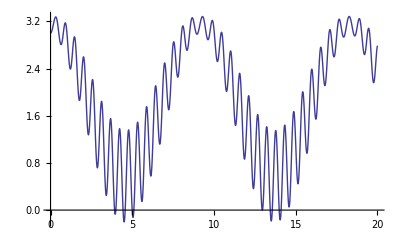

```mathematica
Plot[Evaluate[ExpectedAValue[t]],{t,0,20}]
```

The eigenfrequencies (since we have set ℏ = 1) are

```mathematica
{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3]}=Abs[Eigenvalues[ℍ]]
```

{11.3448,0.515729,0.170915}

So the interference frequencies are

```mathematica
{Subscript[Ω, 1],Subscript[Ω, 2],Subscript[Ω, 3]}={Subscript[ω, 1]-Subscript[ω, 2],Subscript[ω, 1]-Subscript[ω, 3],Subscript[ω, 2]-Subscript[ω, 3]}
```

{10.8291,11.1739,0.344814}

and the associated periods are

```mathematica
{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3]}=(2π)/{Subscript[Ω, 1],Subscript[Ω, 2],Subscript[Ω, 3]}
```

{0.580214,0.562309,18.2219}

which are evident in the figure. 

A time-average of the expected value is given by

```mathematica
Chop[∫_0^20 ExpectedAValue[t]ⅆt]/20
```

1.94261

Here I redraw the figure with gridlines indicating the principal period (τ_3) and preceding time-averaged expected value:

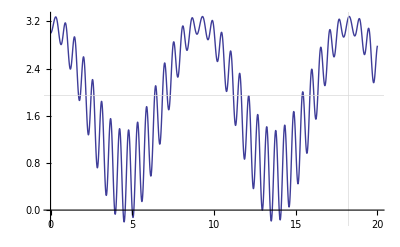

```mathematica
MovingMean=Plot[Evaluate[ExpectedAValue[t]],{t,0,20}, GridLines->{{18.22},{1.94}}]
```

At the moment, I cannot account for the fact that τ_3 appears to be twice the period of the oscillation most evident in the figure.

Here I do some informal "eyeball spectral analysis" of the figure:

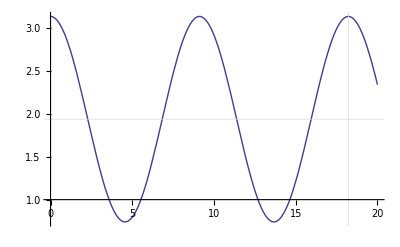

```mathematica
SmoothedApprox=Plot[1.94+1.2Cos[4π t/18.22],{t,0,20}, GridLines->{{18.22},{1.94}}]
```

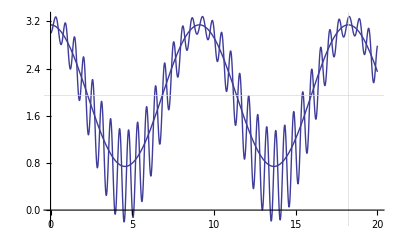

```mathematica
Show[MovingMean,SmoothedApprox]
```

### Effect of altering the initial state:

Suppose we alter the initial state, from (1
0
0) to

```mathematica
Subscript[ψ, 0]=({{0}, {1}, {0}});
```

Proceeding exactly as before…

```mathematica
ψ[t_]:=𝕌[t].Subscript[ψ, 0]
```

```mathematica
MovingExpectedValue[t_]:=(Chop[CompConj[Transpose[ψ[t]]].𝔸.ψ[t]]//Chop)⟦1⟧⟦1⟧
```

```mathematica
ExpectedAValue[t_]:=MovingExpectedValue[t]//Simplify//Chop
```

```mathematica
ExpectedAValue[t]
```

0.987408 Cos[0.170915 t]^2+0.164164 Cos[0.515729 t]^2+0.25431 Cos[0.515729 t] Cos[11.3448 t]+1.277 Cos[11.3448 t]^2+Cos[0.170915 t] (-0.71256 Cos[0.515729 t]+1.02968 Cos[11.3448 t])+0.987408 Sin[0.170915 t]^2+0.71256 Sin[0.170915 t] Sin[0.515729 t]+0.164164 Sin[0.515729 t]^2+1.02968 Sin[0.170915 t] Sin[11.3448 t]-0.25431 Sin[0.515729 t] Sin[11.3448 t]+1.277 Sin[11.3448 t]^2

we are led to this variant of the preceding figure:

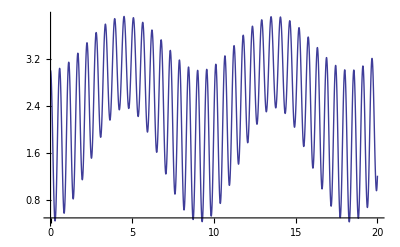

```mathematica
Plot[Evaluate[ExpectedAValue[t]],{t,0,20}]
```

The time-averaged mean assumes a value

```mathematica
Chop[∫_0^20 ExpectedAValue[t]ⅆt]/20
```

2.3779

which differs from its former value (1.94261)

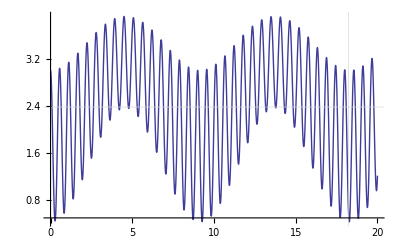

```mathematica
Plot[Evaluate[ExpectedAValue[t]],{t,0,20},GridLines->{{18.22},{2.38}}]
```

### Effect of altering the dimension of the state space:

If the state vector lives in a n-dimensional vector space, then ℍ is n×n. In the absence of spectral degeneracy, the system posseslses n eigenfrequencies

```mathematica
{Subscript[ω, 1],Subscript[ω, 2],...,Subscript[ω, n]}
```

from which one can construct interference frequencies

```mathematica
Subscript[Ω, ij]=Subscript[ω, i]-Subscript[ω, j]
```

that are

```mathematica
f[n_]:=1/2 n(n-1)
```

in number—a number that increases rapidly, and that is equal to n only in the case n = 3:

```mathematica
Table[{n,f[n]},{n,1,10}]//TableForm
```

1 | 0
2 | 1
3 | 3
4 | 6
5 | 10
6 | 15
7 | 21
8 | 28
9 | 36
10 | 45

We therefore expect the motion of the expectation values to become rapidly more complicated as n is increased. Which I illustrate by example:

1.57715 Cos[0.116938 t]^2+0.403776 Cos[0.466295 t]^2+0.0473194 Cos[7.07789 t]^2+Cos[0.116938 t] (0.771648 Cos[0.466295 t]+0.254573 Cos[7.07789 t]-0.241837 Cos[20.7285 t])+Cos[0.466295 t] (-0.0612769 Cos[7.07789 t]-0.139748 Cos[20.7285 t])+0.0120934 Cos[7.07789 t] Cos[20.7285 t]+0.376306 Cos[20.7285 t]^2+1.57715 Sin[0.116938 t]^2-0.771648 Sin[0.116938 t] Sin[0.466295 t]+0.403776 Sin[0.466295 t]^2+0.254573 Sin[0.116938 t] Sin[7.07789 t]+0.0612769 Sin[0.466295 t] Sin[7.07789 t]+0.0473194 Sin[7.07789 t]^2+0.241837 Sin[0.116938 t] Sin[20.7285 t]-0.139748 Sin[0.466295 t] Sin[20.7285 t]-0.0120934 Sin[7.07789 t] Sin[20.7285 t]+0.376306 Sin[20.7285 t]^2

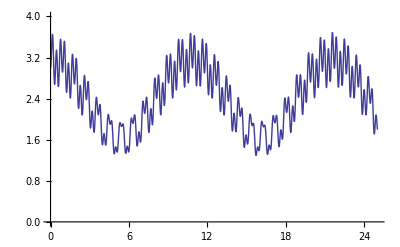

```mathematica
𝔸=({{3, 0, 0, 0}, {0, 3, 2, 1}, {0, 2, 3, 2}, {0, 1, 2, 2}});
Subscript[ψ, 0]=({{1}, {0}, {0}, {0}});
ℍ=({{1., 2., 3., 4.}, {2., 5., 6., 7.}, {3., 6., 8., 9.}, {4., 7., 9., 0.}});
𝕌[t_]:=MatrixExp[-ⅈ ℍ t]

ψ[t_]:=𝕌[t].Subscript[ψ, 0]

MovingExpectedValue[t_]:=(Chop[CompConj[Transpose[ψ[t]]].𝔸.ψ[t]]//Chop)⟦1⟧⟦1⟧

ExpectedAValue[t_]:=MovingExpectedValue[t]//Simplify//Chop

ExpectedAValue[t]

Plot[Evaluate[ExpectedAValue[t]],{t,0,25}, PlotRange->{0,4.0}]
```

```mathematica
{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4]}=Abs[Eigenvalues[ℍ]]

{Subscript[Ω, 1],Subscript[Ω, 2],Subscript[Ω, 3],Subscript[Ω, 4],Subscript[Ω, 5],Subscript[Ω, 6]}={Subscript[ω, 1]-Subscript[ω, 2],Subscript[ω, 1]-Subscript[ω, 3],Subscript[ω, 1]-Subscript[ω, 4],Subscript[ω, 2]-Subscript[ω, 3],Subscript[ω, 2]-Subscript[ω, 4],Subscript[ω, 3]-Subscript[ω, 4]}
```

{20.7285,7.07789,0.466295,0.116938}

{13.6506,20.2622,20.6116,6.6116,6.96096,0.349357}

The curve is—as anticipated—now much more complicated. 

I cannot presently explain why the period most evident in the figure (τ ≈ 11) does not appear in the list of interference periods:

```mathematica
{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4],Subscript[τ, 5],Subscript[τ, 6]}=(2π)/{Subscript[Ω, 1],Subscript[Ω, 2],Subscript[Ω, 3],Subscript[Ω, 4],Subscript[Ω, 5],Subscript[Ω, 6]}
```

{0.460285,0.310093,0.304837,0.950327,0.902632,17.985}